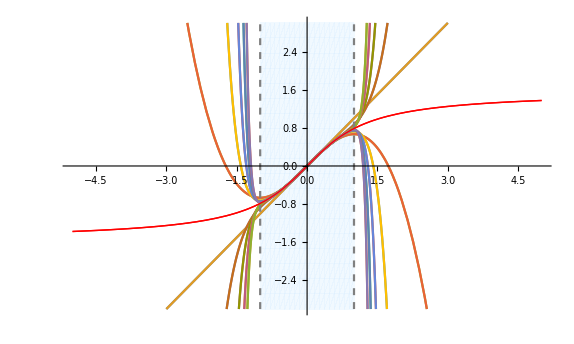

```mathematica
f1=Plot[ArcTan[x],{x,-5,5},AspectRatio->Automatic,PlotStyle->{Red,Thick},PlotRange->3];
f2=Plot[Evaluate[Table[Normal[Series[ArcTan[x],{x,0,n}]],{n,20}]],{x,-3,3},PlotRange->3];
f4=ParametricPlot[{{-1,t},{1,t}},{t,-3,3},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
f3=RegionPlot[-1<x<1,{x,-1,1},{y,-3,3},BoundaryStyle->None,PlotStyle->{LightBlue,Opacity[0.4]}];
Show[f1,f3,f2,f4,f1]
```

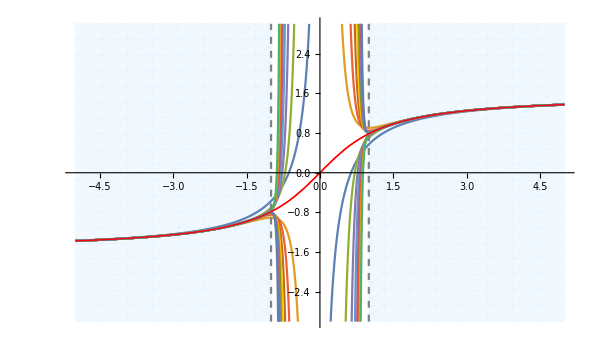

```mathematica
f1=Plot[ArcTan[x],{x,-5,5},AspectRatio->Automatic,PlotStyle->{Red,Thick},PlotRange->3];
f2=Plot[Evaluate[Table[-Pi/2-Sum[(-1)^(n)/((2n+1)x^(2n+1)),{n,0,m}],{m,0,15}]],{x,-5,-0.2},PlotRange->3];
f3=Plot[Evaluate[Table[Pi/2-Sum[(-1)^(n)/((2n+1)x^(2n+1)),{n,0,m}],{m,0,15}]],{x,0.2,5},PlotRange->3];
f4=ParametricPlot[{{-1,t},{1,t}},{t,-3,3},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
f5=RegionPlot[x<-1||x>1,{x,-5,5},{y,-3,3},BoundaryStyle->None,PlotStyle->{LightBlue,Opacity[0.4]}];
Show[f1,f5,f2,f3,f4,f1]
```